### Basic Examples (2)

Check if two expressions are equivalent:

```mathematica
{{-Graphics-, CodeEquivalentQ}}[RandomInteger/@Range[5],Array[RandomInteger,5]]
```

True

View the canonical representations of expressions:

```mathematica
{{-Graphics-, MakeCanonicalForm}}[RandomInteger/@Range[5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,Global`S1∷ℤ}]],{Global`S1∷ℤ,1,5,1}]

```mathematica
{{-Graphics-, MakeCanonicalForm}}[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

These are directly comparable:

```mathematica
%===%%
```

True

### Scope (3)

Get additional information about the equivalence test:

```mathematica
{{-Graphics-, EquivalenceTestData}}[
First[Rest[Range/@Range[2^100]]],
Part[Table[Table[j,{j,i}],{i,2^100}],2]
]
```

<|Timing→<|SameQ→0.,ToCanonicalForm1→1.432998,ToCanonicalForm2→2.202002|>,SameQ→False,CanonicalForms→<|1→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧],2→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

View the sequence of transformations used to convert an expression to its canonical form:

```mathematica
{{-Graphics-, MakeCanonicalForm}}[Array[RandomInteger,5],"Trace"->True]//Column
```

Array[RandomInteger,5]
Table[RandomInteger[S1],{S1,5}]
Table[RandomInteger[S1],{S1,1,5,1}]
Table[RandomInteger[S1∷ℤ],{S1∷ℤ,1,5,1}]
Table[RandomInteger[{0,S1∷ℤ}],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

Convert a canonical representation to a normal expression:

```mathematica
{{-Graphics-, MakeCanonicalForm}}[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

```mathematica
{{-Graphics-, FromCanonicalForm}}[%]
```

Table[RandomVariate[DiscreteUniformDistribution[{0,S1}]],{S1,1,5,1}]

Evaluate:

```mathematica
ReleaseHold[%]
```

{0,1,2,0,4}

### Neat Examples (6)

Here is a list of expressions, some of which are equivalent to others:

```mathematica
expressions={
HoldForm[Table[i,{i,5},{j,i+2}]],
HoldForm[Array[Range,5,3]],
HoldForm[Table[ConstantArray[i,i+2],{i,5}]],
HoldForm[First[Rest[Range/@Range[10]]]],
HoldForm[Range/@Range[3,7]],
HoldForm[Part[Table[Table[j,{j,i}],{i,10}],2]]
};
```

Find the sequence of transformations for each expression:

```mathematica
Short[traces=Most@{{-Graphics-, ToCanonicalForm}}[#,"Trace"->True]&/@expressions]
```

{{Table[i,{i,5},{j,i+2}],Table[Table[S1,{S2,S1+2}],{S1,5}],«4»,Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]},«4»,{«1»}}

Generate a graph for each sequence:

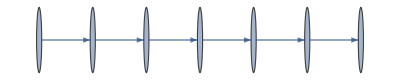
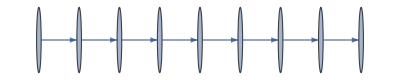
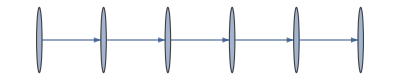
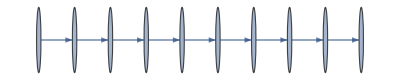
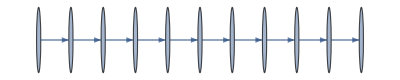
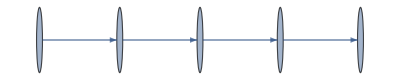

```mathematica
paths=Graph[DirectedEdge@@@Partition[#,2,1]]&/@traces
```

Combine the graphs:

```mathematica
graph=Graph[GraphUnion@@paths,];
```

Equivalent expressions converge to the same connected component:

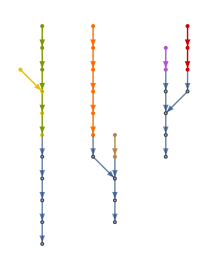

```mathematica
HighlightGraph[graph,paths]
```

Group the expressions into their corresponding equivalence class:

```mathematica
grouped=GroupBy[expressions,{{-Graphics-, ToCanonicalForm}}]
```

<|Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]→{Table[i,{i,5},{j,i+2}],Table[ConstantArray[i,i+2],{i,5}]},Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]→{Array[Range,5,3],Range/@Range[3,7]},Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧→{First[Rest[Range/@Range[10]]],Table[Table[j,{j,i}],{i,10}]⟦2⟧}|>

```mathematica
TableForm[KeyValueMap[Reverse@*List,grouped]]
```

Table[i,{i,5},{j,i+2}]
Table[ConstantArray[i,i+2],{i,5}] | Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]
Array[Range,5,3]
Range/@Range[3,7] | Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]
First[Rest[Range/@Range[10]]]
Table[Table[j,{j,i}],{i,10}]⟦2⟧ | Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧